```mathematica
(* 3.3 Optimal behaviour *)
```

```mathematica
(* 3.3.1 Patient agent *)
```

```mathematica
(* These show the price to rent ratios necessary for non-zero finite housing investment *)
```

```mathematica
Solve[1/βp==1+(m-p*δ)/p,p]//Simplify
```

{{p→(m βp)/(1+βp (-1+δ))}}

```mathematica
Solve[1/βp==1+(m-p*δ)/p,m]//Simplify
```

{{m→p (-1+1/βp+δ)}}

```mathematica
(* 3.3.2 Impatient agent decision rule
Given prices, rents and interest rates the impatient agent must decide whether to rent or buy, and how much housing to consume *)
```

```mathematica
(* Owner occupier *)
```

```mathematica
LagrangianOO[n_]:=Sum[βi^t*(Subscript[ci, t]+vbOO[Subscript[hi, t]]),{t,0,n}]+Sum[-Subscript[λi, t]*βi^t(Subscript[ci, t]+Subscript[p, t]*(Subscript[hi, t+1]-(1-δ)*Subscript[hi, t])+Subscript[r, t-1]*Subscript[di, t-1]-Subscript[y, t]-Subscript[di, t]),{t,0,n}]+
Sum[-Subscript[μ, t]*βi^t*(Subscript[di, t]-θ*Subscript[p, t]*Subscript[hi, t+1]),{t,0,n}]
```

```mathematica
focOO=Grad[LagrangianOO[Infinity],{Subscript[ci, 0],Subscript[ci, 1],Subscript[hi, 1],Subscript[di, 0],Subscript[μ, 0],Subscript[λi, 0]}];
MatrixForm[focOO]//Simplify
```

(1-λi_0
βi-βi λi_1
p_0 (-λi_0+θ μ_0)+βi (-(-1+δ) p_1 λi_1+vbOO'[hi_1])
λi_0-βi r_0 λi_1-μ_0
-di_0+θ hi_1 p_0
-ci_0+di_0+hi_0 p_0-δ hi_0 p_0-hi_1 p_0-di_-1 r_-1+y_0)

```mathematica
eq1=Eliminate[focOO[[1]]==0&&focOO[[2]]==0&&focOO[[4]]==0,{Subscript[λi, 0],Subscript[λi, 1]}]//Simplify 
eq2=Eliminate[focOO[[1]]==0&&focOO[[2]]==0&&focOO[[3]]==0,{Subscript[λi, 0],Subscript[λi, 1]}]//Simplify 
eq3=focOO[[5]]==0
eq4=focOO[[6]]==0
```

βi r_0+μ_0==1

βi (-1+δ) p_1+p_0 (1-θ μ_0)==βi vbOO'[hi_1]

-di_0+θ hi_1 p_0==0

-ci_0+di_0+hi_0 p_0-δ hi_0 p_0-hi_1 p_0-di_-1 r_-1+y_0==0

```mathematica
(* Optimal policy *)
```

```mathematica
s1subst={Subscript[p, 0]->p,Subscript[p, 1]->p};
{{dTstar,mrsOstar,cOstar,μOstar}}={Subscript[di, 0],vbOO'[Subscript[hi, 1]],Subscript[ci, 0],Subscript[μ, 0]}/.Solve[Evaluate[{eq1,eq2,eq3,eq4}/.s1subst],{Subscript[di, 0],vbOO'[Subscript[hi, 1]],Subscript[ci, 0],Subscript[μ, 0]}]//Simplify
```

{{p θ hi_1,(p (1+βi (-1+δ)-θ+βi θ r_0))/βi,(p-p δ) hi_0+p (-1+θ) hi_1-di_-1 r_-1+y_0,1-βi r_0}}

```mathematica
mrsOstar (* Optimal housing decisions given price p and interet rate Subscript[r, 0]*)
```

(p (1+βi (-1+δ)-θ+βi θ r_0))/βi

```mathematica
(* Note:  if that led to Subscript[ci, 0]<0, (i.e. agent does not have sufficient deposit)the following would be the optimal feasible policy.  *)
```

```mathematica
Solve[Evaluate[{eq1,eq2,eq3,Subscript[ci, 0]==0}/.s1subst],{Subscript[di, 0],vbOO'[Subscript[hi, 1]],Subscript[ci, 0],Subscript[μ, 0]}]//Simplify
```

{{di_0→p θ hi_1,vbOO'[hi_1]→(p (1+βi (-1+δ)-θ+βi θ r_0))/βi,ci_0→0,μ_0→1-βi r_0}}

```mathematica
(* Tenant *)
```

```mathematica
LagrangianT[n_]:=Sum[βi^t*(Subscript[ci, t]+vbT[Subscript[hi, t]]),{t,0,n}]+Sum[-Subscript[λi, t]*βi^t(Subscript[ci, t]+Subscript[m, t]*Subscript[hi, t+1]-Subscript[y, t]),{t,0,n}]
```

```mathematica
focT=Grad[LagrangianT[Infinity],{Subscript[ci, 0],Subscript[ci, 1],Subscript[hi, 1],Subscript[λi, 0]}];
MatrixForm[focT]//Simplify
```

(1-λi_0
βi-βi λi_1
-m_0 λi_0+βi vbT'[hi_1]
-ci_0-hi_1 m_0+y_0)

```mathematica
eq1T=Eliminate[focT[[1]]==0&&focT[[2]]==0&&focT[[3]]==0,{Subscript[λi, 0],Subscript[λi, 1]}]//Simplify 
eq2T=focT[[4]]==0
```

m_0==βi vbT'[hi_1]

-ci_0-hi_1 m_0+y_0==0

```mathematica
s2subst={Subscript[p, 0]->p,Subscript[p, 1]->p};
{{mrsTstar,cTstar}}={vbT'[Subscript[hi, 1]],Subscript[ci, 0]}/.Solve[Evaluate[{eq1T,eq2T}/.s2subst],{vbT'[Subscript[hi, 1]],Subscript[ci, 0]}]//Simplify
```

{{m_0/βi,-hi_1 m_0+y_0}}

```mathematica
(* Agent compares the optimal choice for Owner-occ and for Tenant, then selects the best one. *)
```

```mathematica
{{indifP}}={p}/.Solve[Evaluate[βi/(1-βi)*(cOstar+vbOO[hOstar])==(1-θ)*p*hOstar+βi/(1-βi)*(cTstar+vbT[hTstar])/.Subscript[di, -1]->θ*p*hOstar],p]//Simplify
```

{{(βi (hi_1 m_0+vbOO[hOstar]-vbT[hTstar]))/(hOstar (-1+βi) (-1+θ)+βi (-1+δ) hi_0+(βi-βi θ) hi_1+hOstar βi θ r_-1)}}

```mathematica
indifP/.hOstar->hbar/.hTstar->hbar/.Subscript[hi, 0]->hbar/.Subscript[hi, 1]->hbar//Simplify
```

(βi (hbar m_0+vbOO[hbar]-vbT[hbar]))/(hbar (1+βi (-1+δ)-θ+βi θ r_-1))

```mathematica
(* 4 Types of Equilibrium *)
```

```mathematica
Clear[vO]
Clear[vT]
uO=βi/(1-βi)*((cO)+vO[hO]);
uT=(1-θ)*p*hO+βi/(1-βi)*(cT+vT[hT]);
ineqOT=uO==uT;
```

```mathematica
vO[h_]:=Log[h]
vT[h_]:=Log[h]+logω (* NB. I use logω rather than Log[ω] to make the equation solving simpler *)
```

```mathematica
(* Alternative U
  vO[h_]:=h^(1/2)
vT[h_]:=(ω*h)^(1/2)  *)
```

```mathematica
(* 4.3 Equilibria with unconstrained lending *)
R->1/βp
```

R→1/βp

```mathematica
(*  4.3.1 All OO with unconstrained lending *)
```

```mathematica
(* Optimal behaviour for a deviating owner to become a tenant: *)
```

```mathematica
{{hTstar}}={hT}/.Solve[D[vT[hT],hT]==m/βi,hT]
```

{{βi/m}}

```mathematica
(* Market clearing price assuming all OO: *)
```

```mathematica
{{pBconO}}={p}/.Solve[D[vO[hO],hO]==p*(1-βi*(1-δ)-θ*(1-βi*R))/βi,p]/.R->1/βp/.hO->hbar//Simplify
```

{{(βi βp)/(hbar (βp+βi βp (-1+δ)+βi θ-βp θ))}}

```mathematica
(* Finding Log[ω] threshold that enables this OO equilibrium *)
```

```mathematica
{{logωThreshO}}={logω}/.Solve[Evaluate[{ineqOT}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.m->p*(1-βp*(1-δ))/βp
/.p->pBconO
/.R->1/βp
/.hO->hbar
/.hbar->1],{logω}]//Simplify
```

{{-1+βi-Log[(βp+βi βp (-1+δ)+βi θ-βp θ)/(1+βp (-1+δ))]}}

```mathematica
(* 4.3.3 All tentants *)
```

```mathematica
(* Finding optimal hosuing for a deviating tenant to owner *)
{{hOstar}}={hO}/.Solve[D[vO[hO],hO]==p*(1-βi*(1-δ)-θ*(1-βi*R))/βi,hO]
```

{{βi/(p (1-βi+βi δ-θ+R βi θ))}}

```mathematica
{{logωThreshT}}={logω}/.Solve[Evaluate[{ineqOT}

/.cO->y-p*hO*(θ*(R-1)+δ)
/.hO->hOstar
/.cT ->y-m*hT
/.p->(m*βp)/(1-βp*(1-δ))
/.m->D[vO[hbar],hbar]*βi 
/.R->1/βp
/.hT->hbar
/.hbar->1],{logω}]//Simplify
```

{{-1+βi+Log[(1+βp (-1+δ))/(βp+βi βp (-1+δ)+βi θ-βp θ)]}}

```mathematica
pBconT=p/.p->(m*βp)/(1-βp*(1-δ))/.m->D[vO[hbar],hbar]*βi
```

(βi βp)/(hbar (1-βp (1-δ)))

```mathematica
(* 4.4 Equilibrium with constrained Lending *)
```

```mathematica
(* 4.4.1 Unconstrained borrowing *)
```

```mathematica
(* Lbar<(βi θ)/(1+βi (-1+δ))*)
```

```mathematica
(* All owner equilibrium requires ω lower than the following, where Lending constraint binds and collateral does not *)
```

```mathematica
{{logωThLbindBnotO}}={logω}/.Solve[Evaluate[{ineqOT}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.m->p*(1-βp*(1-δ))/βp
/.p->(vO'[hO]*βi)/(1-βi*(1-δ))
/.R->1/βi
/.hO->hbar
/.hbar->1],{logω}]//Simplify
```

{{-1+βi-Log[(βp+βi βp (-1+δ))/(1+βp (-1+δ))]}}

```mathematica
Exp[logωThLbindBnotO]//Simplify
```

(ⅇ^(-1+βi) (1+βp (-1+δ)))/(βp+βi βp (-1+δ))

```mathematica
pLconO=p/.p->(vO'[hbar]*βi)/(1-βi*(1-δ))
```

βi/(hbar (1-βi (1-δ)))

```mathematica
(* but if ω is above that threshold, some households will rent. That slackens the lending constraint so other households can borrow more. Now both cosntraints will bind *)
```

```mathematica
ineqOTω=(βi (cO+Log[hO]))/(1-βi)==hO p (1-θ)+(βi (cT+Log[ω]+Log[hT]))/(1-βi)
 (* rewriting indifference eq in terms of ω rather than Log[ω] to make solutions clearer below *)
```

(βi (cO+Log[hO]))/(1-βi)==hO p (1-θ)+(βi (cT+Log[hT]+Log[ω]))/(1-βi)

```mathematica
{{RLbindIntω,χLbindIntω,pLbindIntω}}={R,χ,p}/.Solve[Evaluate[{ineqOTω,χ*hO+(1-χ)*hT==hbar,p==lbar/(χ*θ*hO)}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.hO->hOstar
/.m->p*(1-βp*(1-δ))/βp
/.hbar->hbar],{R,χ,p}]//Simplify
```

{{(ⅇ^βi (1+βp (-1+δ))+ⅇ βp (-1+βi-βi δ+θ) ω)/(ⅇ βi βp θ ω),(ⅇ^(-1+βi) (lbar+lbar βp (-1+δ)))/(βi βp θ ω),(lbar+(βi βp θ)/(1+βp (-1+δ))-(ⅇ^(-1+βi) lbar)/ω)/(hbar θ)}}

```mathematica
Simplify[Reduce[{χLbindIntω<1},{lbar},Reals],Assumptions->{βp>0,βi>0,δ>0,δ<1,βp<1,βi<1,lbar>0,θ>0,θ<1,βi<βp,ω>0,ω<1}]
```

ⅇ^βi lbar (1+βp (-1+δ))<ⅇ βi βp θ ω

```mathematica
(* 4.4.2 Both lending and collateral bind in all owner-occupier eq: (βi θ)/(1+βi (-1+δ))<lbar<(βi βp θ)/(βp+βi βp (-1+δ)+βi θ-βp θ) *)
```

```mathematica
(* If all impatient households own then the threshold ω and the market clearing interest rate are: *)
```

```mathematica
{{logωThLbothBind,Rbothbind}}={logω,R}/.Solve[Evaluate[{ineqOT,hO==hOstar}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.m->p*(1-βp*(1-δ))/βp
/.p->lbar/(θ*hO)
/.hO->hbar
/.hbar->hbar],{logω,R}]//Simplify
```

{{-1+βi+Log[hbar]-Log[(hbar βi βp θ)/(lbar+lbar βp (-1+δ))],1/lbar+(-1+βi-βi δ+θ)/(βi θ)}}

```mathematica
(* Note that the feasible bounds on R show the bounds on this type of equilibrium *)
Simplify[Reduce[1/βp<Rbothbind<1/βi,lbar],Assumptions->{βp>0,βi>0,δ>0,δ<1,βp<1,βi<1,lbar>0,θ>0,θ<1,βi<βp}]
```

(βi θ)/(1+βi (-1+δ))<lbar<(βi βp θ)/(βp+βi βp (-1+δ)+βi θ-βp θ)

```mathematica
pBothconO=p/.p->lbar/(θ*hbar)
```

lbar/(hbar θ)

```mathematica
(* What if the rental penalty is small enough to preclude the above eq but not small enough to allow the full tenant equilibrium? I.e. Exp[logωThreshT]>ω>Exp[logωThLbothBind]

Again we need some impatient households to rent to slacken the lending constraint *)
```

```mathematica
Exp[logωThreshT]>ω>Exp[logωThLbothBind]//Simplify
```

(ⅇ^(-1+βi) (1+βp (-1+δ)))/(βp+βi βp (-1+δ)+βi θ-βp θ)>ω>(ⅇ^(-1+βi) (lbar+lbar βp (-1+δ)))/(βi βp θ)

```mathematica
(* This finds market clearing price and R for a given χ when the lending cosntraint is binding and borrowers borrow up to their constraint *)
{{RLintBothB,PLintBothBSolve}}={R,p}/.Solve[Evaluate[{χ*hO+(1-χ)*hT==hbar,p==lbar/(χ*θ*hO)}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.hO->hOstar
/.m->p*(1-βp*(1-δ))/βp],{R,p}]//Simplify
```

{{(-1+βi-βi δ+θ)/(βi θ)+χ/lbar,(lbar+lbar βp (-1+δ)-βi βp θ (-1+χ))/(hbar (1+βp (-1+δ)) θ)}}

```mathematica
(* Same procedure but wrt R and χ, to then find bounds on p*)
{{Rbound,χbound}}={R,χ}/.Solve[Evaluate[{χ*hO+(1-χ)*hT==hbar,p==lbar/(χ*θ*hO)}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.hO->hOstar
/.m->p*(1-βp*(1-δ))/βp],{R,χ}]//Simplify
```

{{(lbar+βi βp θ-hbar p (1+βp (-1+δ)) θ+lbar βp (-2+βi+δ-βi δ+θ))/(lbar βi βp θ),(lbar+lbar βp (-1+δ)+βi βp θ-hbar p (1+βp (-1+δ)) θ)/(βi βp θ)}}

```mathematica
Simplify[Reduce[Evaluate[{1/βp<Rbound<1/βi}/.hbar->1],p],Assumptions->{p>0,βp>0,βi>0,δ>0,δ<1,βp<1,βi<1,lbar>1,θ>0,θ<1,βi<βp}]
```

(lbar+lbar βp (-2+βi+δ-βi δ)+βi βp θ)/(θ+βp (-1+δ) θ)<p<(lbar-lbar βi θ+βi βp θ+lbar βp (-2+βi+δ-βi δ+θ))/(θ+βp (-1+δ) θ)

```mathematica
Simplify[Reduce[Evaluate[{0<χbound<1}/.hbar->1],p],Assumptions->{p>0,βp>0,βi>0,δ>0,δ<1,βp<1,βi<1,lbar>1,θ>0,θ<1,βi<βp}]
```

lbar/θ<p<(lbar+lbar βp (-1+δ)+βi βp θ)/(θ+βp (-1+δ) θ)

```mathematica
LowP=Max[lbar/θ,(lbar+lbar βp (-2+βi+δ-βi δ)+βi βp θ)/(θ+βp (-1+δ) θ)];
HighP=Min[(lbar+lbar βp (-1+δ)+βi βp θ)/(θ+βp (-1+δ) θ),(lbar-lbar βi θ+βi βp θ+lbar βp (-2+βi+δ-βi δ+θ))/(θ+βp (-1+δ) θ)];
```

```mathematica
(* 5. Calibrated examples *)
(* Need to define some important thresholds *)
```

```mathematica
(*Lbar thresholds *)
Llow=(βi θ)/(1+βi (-1+δ));
Lhigh=(βi βp θ)/(βp+βi βp (-1+δ)+βi θ-βp θ);
Lmid=Mean[{Llow,Lhigh}];
```

```mathematica
(* ω thresholds *)
ωlow=Exp[logωThLbindBnotO];
ωhighθ=Exp[logωThreshO];
ωmidLθ=Exp[logωThLbothBind];
```

```mathematica
(* JPT params *)
JPTparams={βp->0.975,βi->0.95,δ->0.012};
```

```mathematica
(* Note: for the range equilibrium, I will take the midpoint as by numerical answer for now *)
prange=Mean[{LowP,HighP}];
Rrange=Rbound/.p->prange;
χrange=χbound/.p->prange;
```

```mathematica
(* Shows the L̄ and ω thresholds as a function of θ *)
```

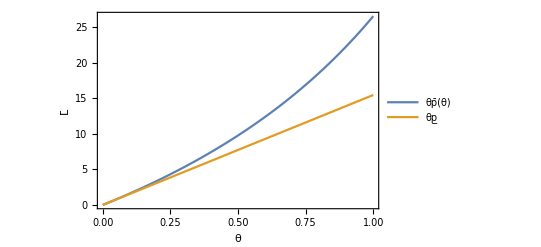

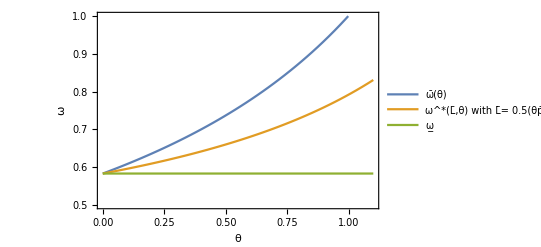

```mathematica
Plot[Evaluate[{Lhigh,Llow}/.JPTparams/.hbar->1],{θ,0.0,1},PlotLegends->Placed[{"θp̄(θ)", "θp̲"},Center ],Frame->True,FrameLabel->{"θ","L̄","Threshold lending constraint, L̄"}]
Plot[Evaluate[{ωhighθ,ωmidLθ,ωlow}/.lbar->Lmid/.JPTparams/.hbar->1],{θ,0,1.1},PlotLegends->Placed[{"ω̄(θ)", "ω^*(L̄,θ) with L̄= 0.5(θp̄(θ)+θp̲)","ω̲"},Center ],PlotRange->{.5,1},Frame->True,FrameLabel->{"θ","ω","Threshold rental penalty in different equilibria"}]
```

```mathematica
(* Define four ω values to explore the parameter space *)
{Highestω, Higherω,Lowerω,Lowestω}=Round[Evaluate[{ωhighθ+.01,(2*ωhighθ+ωlow)/3,(ωhighθ+2*ωlow)/3,ωlow-0.01}/.θ->0.8/.JPTparams/.hbar->1],0.01]
```

{0.89,0.78,0.68,0.57}

```mathematica
(* Evaluating the equilibrium variables as a function of parameters. *)
```

```mathematica
(* Price: (rent-price ratio is constant so this also gives rent) *)
eqPrice[Lbar_,θ_,ω_]:=Piecewise[{
{pLconO,Lbar<pLconO*θ*hbar&&ω<ωlow},
{pBothconO,pLconO*θ*hbar<Lbar<θ*hbar*pBconO && ω<ωlow},
{pBconO,Lbar>θ*hbar*pBconO &&ω<ωhighθ},
{pLbindIntω,Lbar<pLconO*θ*hbar&&ωlow<ω<ωhighθ},
{pBconT,ω>ωhighθ},
{pBothconO,pLconO*θ*hbar<Lbar<θ*hbar*pBconO && ωlow<ω<ωmidLθ},
{prange,pLconO*θ*hbar<Lbar<θ*hbar*pBconO &&ωmidLθ<ω<ωhighθ}
}]
```

```mathematica
(* Allocation of tentant vs owner*)
eqχ[Lbar_,θ_,ω_]:=Piecewise[{
{1,ω<ωlow},
{0,ω>ωhighθ},
{1,Lbar>θ*hbar*pBconO &&ω<ωhighθ},
{χLbindIntω,Lbar<pLconO*θ*hbar&&ωlow<ω<ωhighθ},
{1,pLconO*θ*hbar<Lbar<θ*hbar*pBconO && ωlow<ω<ωmidLθ},
{χrange,pLconO*θ*hbar<Lbar<θ*hbar*pBconO &&ωmidLθ<ω<ωhighθ}
}]
```

```mathematica
(* Interest rate *)
eqR[Lbar_,θ_,ω_]:=Piecewise[{
{1/βi,Lbar<pLconO*θ*hbar&&ω<ωlow},
{Rbothbind,pLconO*θ*hbar<Lbar<θ*hbar*pBconO && ω<ωlow},
{1/βp,Lbar>θ*hbar*pBconO &&ω<ωhighθ},
{RLbindIntω,Lbar<pLconO*θ*hbar&&ωlow<ω<ωhighθ},
{1/βp,ω>ωhighθ},
{Rbothbind,pLconO*θ*hbar<Lbar<θ*hbar*pBconO && ωlow<ω<ωmidLθ},
{Rrange,pLconO*θ*hbar<Lbar<θ*hbar*pBconO &&ωmidLθ<ω<ωhighθ}
}]
```

```mathematica
(* Debt  *)
eqD[Lbar_,θ_,ω_]:=Piecewise[{
{Lbar,Lbar<pLconO*θ*hbar&&ω<ωlow},
{Lbar,pLconO*θ*hbar<Lbar<θ*hbar*pBconO && ω<ωlow},
{pBconO*hbar*θ,Lbar>θ*hbar*pBconO &&ω<ωhighθ},
{Lbar/χLbindIntω,Lbar<pLconO*θ*hbar&&ωlow<ω<ωhighθ},
{0,ω>ωhighθ},
{Lbar,pLconO*θ*hbar<Lbar<θ*hbar*pBconO && ωlow<ω<ωmidLθ},
{Lbar/χrange,pLconO*θ*hbar<Lbar<θ*hbar*pBconO &&ωmidLθ<ω<ωhighθ}
}]
```

```mathematica
(* Graphing the variables against Lbar for different ω values*)
```

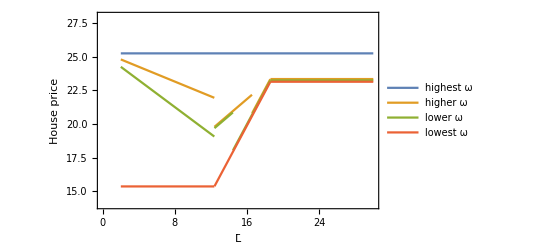

```mathematica
Plot[Evaluate[{eqPrice[lbar,θ,Highestω],Evaluate[eqPrice[lbar,θ,Higherω]/.ω->Higherω]+.1,Evaluate[eqPrice[lbar,θ,Lowerω]/.ω->Lowerω],eqPrice[lbar,θ,Lowestω]-0.1}/.θ->0.8/.JPTparams/.hbar->1],{lbar,2,30},PlotLegends->Placed[{"highest ω", "higher ω","lower ω", "lowest ω"},Bottom ],PlotRange->{14,28},Frame->True,FrameLabel->{"L̄","House price","Effects of lending constraints  with different ω"}]
```

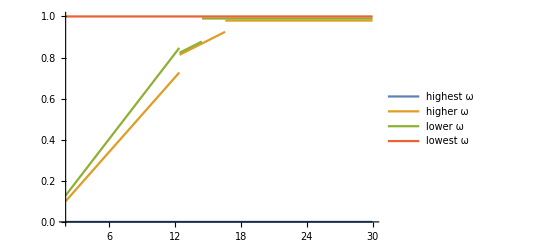

```mathematica
Plot[Evaluate[{eqχ[lbar,θ,Highestω],Evaluate[eqχ[lbar,θ,Higherω]/.ω->Higherω]-.02,Evaluate[eqχ[lbar,θ,Lowerω]/.ω->Lowerω]-.01,eqχ[lbar,θ,Lowestω]}/.θ->0.8/.JPTparams/.hbar->1],{lbar,2,30},PlotLegends->{"highest ω", "higher ω","lower ω", "lowest ω"}]
```

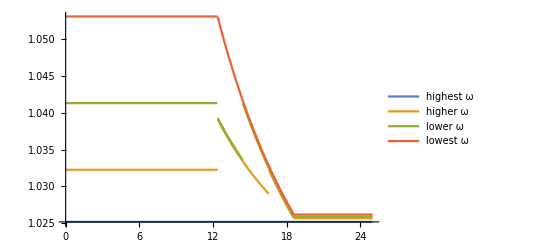

```mathematica
Plot[Evaluate[{eqR[lbar,θ,Highestω]-0.0005,Evaluate[eqR[lbar,θ,Higherω]/.ω->Higherω],Evaluate[eqR[lbar,θ,Lowerω]/.ω->Lowerω]+0.0002,eqR[lbar,θ,Lowestω]+0.0005}/.θ->0.8/.JPTparams/.hbar->1],{lbar,0,25},PlotLegends->{"highest ω", "higher ω","lower ω", "lowest ω"}]
```

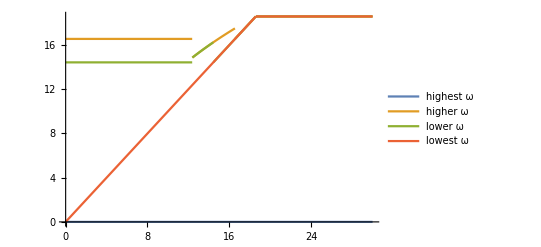

```mathematica
Plot[Evaluate[{eqD[lbar,θ,Highestω],Evaluate[eqD[lbar,θ,Higherω]/.ω->Higherω],Evaluate[eqD[lbar,θ,Lowerω]/.ω->Lowerω],eqD[lbar,θ,Lowestω]}/.θ->0.8/.JPTparams/.hbar->1],{lbar,0,30},PlotLegends->{"highest ω", "higher ω","lower ω", "lowest ω"}]
```

```mathematica
(* Same graphs as a function of θ *)
```

```mathematica
(* These are a bit harder to think about because the L and ω thresholds both depend on θ. This means the equilibrium you are in can flip a lot *)
```

```mathematica
(* L thresholds *)
```

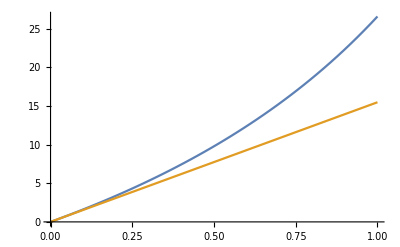

```mathematica
Plot[Evaluate[{Lhigh,Llow}/.JPTparams/.hbar->1],{θ,0.0,1}]
```

```mathematica
(* ω thresholds *)
```

```mathematica
ωlow=Exp[logωThLbindBnotO];
ωhighθ=Exp[logωThreshO];
ωmidLθ=Exp[logωThLbothBind];
```

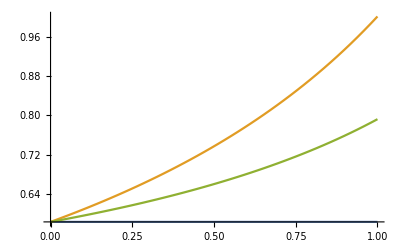

```mathematica
Plot[Evaluate[{ωlow,ωhighθ,ωmidLθ}/.lbar->Lmid/.JPTparams/.hbar->1],{θ,0.0,1}]
```

```mathematica
(* Price with never-binding Lending constraint *)
```

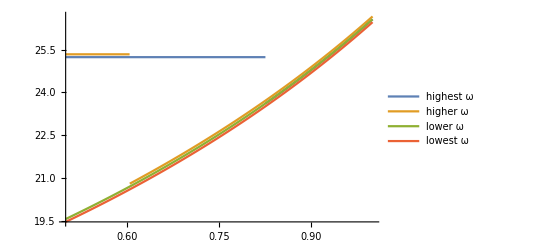

```mathematica
Plot[Evaluate[{eqPrice[lbar,θ,Highestω],Evaluate[eqPrice[lbar,θ,Higherω]/.ω->Higherω]+.1,Evaluate[eqPrice[lbar,θ,Lowerω]/.ω->Lowerω],eqPrice[lbar,θ,Lowestω]-0.1}/.lbar->40/.JPTparams/.hbar->1],{θ,0.5,1},PlotLegends->{"highest ω", "higher ω","lower ω", "lowest ω"}]
```

15.4828

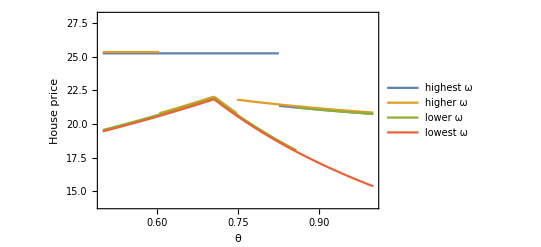

```mathematica
(* Price mid-range Lending constraint. This has the weird feature that loosening the coolateral constraint can lower prices (in the equilibrium where both constraints bind). This is a feature of JPT too, see red line with lowest ω. *)
exampleLbar=Lmid/.JPTparams/.θ->.8
Plot[Evaluate[{eqPrice[lbar,θ,Highestω],Evaluate[eqPrice[lbar,θ,Higherω]/.ω->Higherω]+.1,Evaluate[eqPrice[lbar,θ,Lowerω]/.ω->Lowerω],eqPrice[lbar,θ,Lowestω]-0.1}/.lbar->exampleLbar/.JPTparams/.hbar->1],{θ,0.5,1},PlotLegends->Placed[{"highest ω", "higher ω","lower ω", "lowest ω"},Bottom ],PlotRange->{14,28},Frame->True,FrameLabel->{"θ","House price","Effects of collateral constraints with different ω"}]
```

```mathematica
(* Allocation with intermediate L.The lending constraint starts binding at high levels of θ *)
```

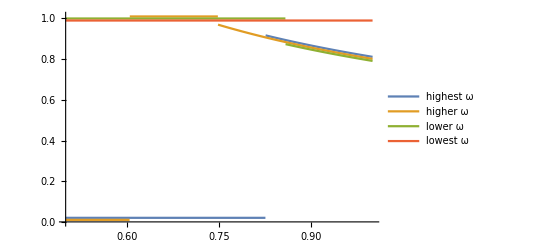

```mathematica
Plot[Evaluate[{eqχ[lbar,θ,Highestω]+.02,Evaluate[eqχ[lbar,θ,Higherω]/.ω->Higherω]+.01,Evaluate[eqχ[lbar,θ,Lowerω]/.ω->Lowerω],eqχ[lbar,θ,Lowestω]-0.01}/.lbar->exampleLbar/.JPTparams/.hbar->1],{θ,0.5,1},PlotLegends->{"highest ω", "higher ω","lower ω", "lowest ω"}]
```

```mathematica
(* R with intermediate L.R rises as lending constraint starts binding at high levels of θ
```

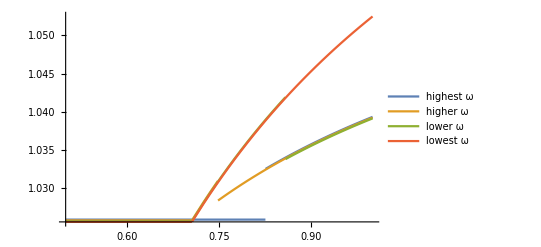

```mathematica
Plot[Evaluate[{eqR[lbar,θ,Highestω]+.0002,Evaluate[eqR[lbar,θ,Higherω]/.ω->Higherω]+.0001,Evaluate[eqR[lbar,θ,Lowerω]/.ω->Lowerω],eqR[lbar,θ,Lowestω]-0.0001}/.lbar->exampleLbar/.JPTparams/.hbar->1],{θ,0.5,1},PlotLegends->{"highest ω", "higher ω","lower ω", "lowest ω"}]
```

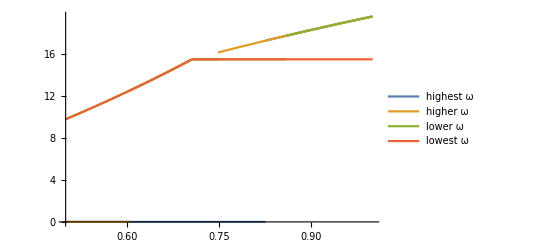

```mathematica
(* D with intermediate L *)
Plot[Evaluate[{eqD[lbar,θ,Highestω]+.0002,Evaluate[eqD[lbar,θ,Higherω]/.ω->Higherω]+.0001,Evaluate[eqD[lbar,θ,Lowerω]/.ω->Lowerω],eqD[lbar,θ,Lowestω]-0.0001}/.lbar->exampleLbar/.JPTparams/.hbar->1],{θ,0.5,1},PlotLegends->{"highest ω", "higher ω","lower ω", "lowest ω"}]
```

```mathematica
(* JPTs calibrated scenario starts in 2000 ends in 2006 *)
(* THey start with θ=0.8 and gradually loosen to 1.02. 
They start with Lbar<θ*p*hbar. Then increase L until it no longer binds 
start at Lbar= θ p̲ hbar then rise linearly to θ p̄(θ)hbar. *)
```

```mathematica
θstart=0.8;
θend=1.02;
```

```mathematica
Lstart=Llow/.θ->θstart/.JPTparams
Lend=Lhigh/.θ->θend/.JPTparams
```

12.3779

27.4924

```mathematica
years=6;
Lincrement=(Lend-Lstart)/years;
θincrement=(θend-θstart)/years;
```

```mathematica
θmov=θstart+t*θincrement;
Lmov=Lstart+t*Lincrement;
```

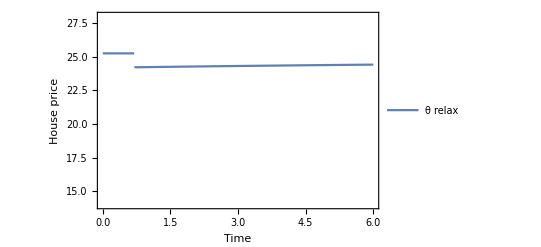

```mathematica
plotP1=Plot[Evaluate[{
Evaluate[eqPrice[lbar,θmov,Highestω]/.lbar->Lstart/.θ->θmov]

}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Highestω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{14,28},Frame->True,FrameLabel->{"Time","House price","Effects of relaxing constraints with High ω"}]
```

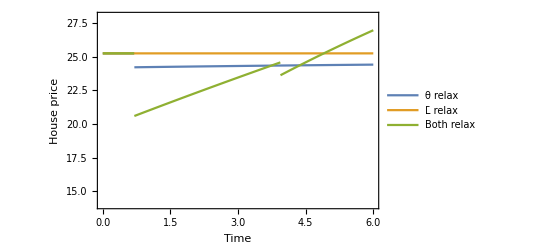

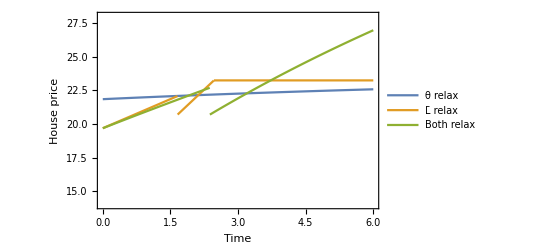

```mathematica
plotP1=Plot[Evaluate[{
Evaluate[eqPrice[lbar,θmov,Highestω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqPrice[Lstart+t*Lincrement,θ,Highestω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqPrice[Lmov,θmov,Highestω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Highestω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{14,28},Frame->True,FrameLabel->{"Time","House price","Effects of relaxing constraints with High ω"}]
plotP2=Plot[Evaluate[{
Evaluate[eqPrice[lbar,θmov,Higherω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqPrice[Lstart+t*Lincrement,θ,Higherω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqPrice[Lmov,θmov,Higherω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Higherω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{14,28},Frame->True,FrameLabel->{"Time","House price","Effects of relaxing constraints with Intermediate ω"}]
plotP3=Plot[Evaluate[{
Evaluate[eqPrice[lbar,θmov,Lowestω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqPrice[Lstart+t*Lincrement,θ,Lowestω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqPrice[Lmov,θmov,Lowestω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Lowestω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{14,28},Frame->True,FrameLabel->{"Time","House price","Effects of relaxing constraints with Low ω"}]
```

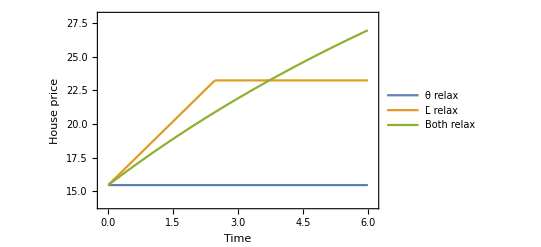

```mathematica
plotR1=Plot[Evaluate[{
Evaluate[eqR[lbar,θmov,Highestω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqR[Lstart+t*Lincrement,θ,Highestω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqR[Lmov,θmov,Highestω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Highestω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{1.02,1.06},Frame->True,FrameLabel->{"Time","R","Effects of relaxing constraints with High ω"}]
plotR2=Plot[Evaluate[{
Evaluate[eqR[lbar,θmov,Higherω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqR[Lstart+t*Lincrement,θ,Higherω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqR[Lmov,θmov,Higherω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Higherω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{1.02,1.06},Frame->True,FrameLabel->{"Time","R","Effects of relaxing constraints with Intermediate ω"}]
plotR3=Plot[Evaluate[{
Evaluate[eqR[lbar,θmov,Lowestω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqR[Lstart+t*Lincrement,θ,Lowestω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqR[Lmov,θmov,Lowestω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Lowestω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{1.02,1.06},Frame->True,FrameLabel->{"Time","R","Effects of relaxing constraints with Low ω"}]
```

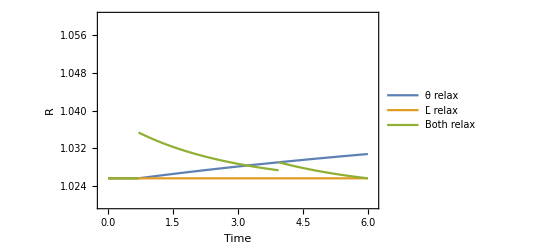

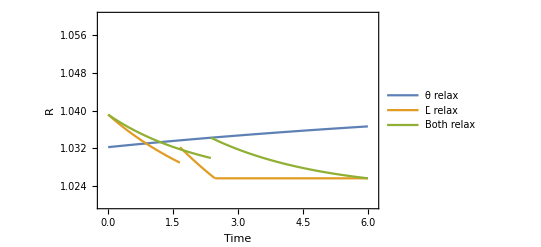

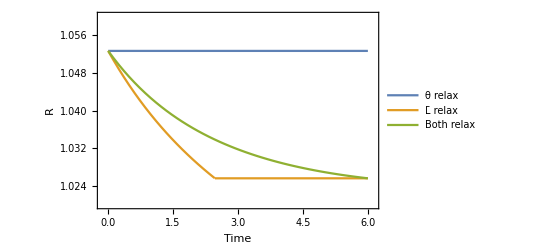

```mathematica
plotχ1=Plot[Evaluate[{
Evaluate[eqχ[lbar,θmov,Highestω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqχ[Lstart+t*Lincrement,θ,Highestω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqχ[Lmov,θmov,Highestω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Highestω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{-0.1,1.1},Frame->True,FrameLabel->{"Time","χ","Effects of relaxing constraints with High ω"}]
plotχ2=Plot[Evaluate[{
Evaluate[eqχ[lbar,θmov,Higherω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqχ[Lstart+t*Lincrement,θ,Higherω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqχ[Lmov,θmov,Higherω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Higherω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{-0.1,1.1},Frame->True,FrameLabel->{"Time","χ","Effects of relaxing constraints with Intermediate ω"}]
plotχ3=Plot[Evaluate[{
Evaluate[eqχ[lbar,θmov,Lowestω]/.lbar->Lstart/.θ->θmov],
Evaluate[eqχ[Lstart+t*Lincrement,θ,Lowestω]/.θ->θstart/.lbar->Lmov],
Evaluate[eqχ[Lmov,θmov,Lowestω]/.lbar->Lmov/.θ->θmov]
}/.θ->θstart+t*θincrement/.JPTparams/.hbar->1/.ω->Lowestω],{t,0,years},PlotLegends->Placed[{"θ relax ","L̄ relax", "Both relax            "},Center ],PlotRange->{-0.1,1.1},Frame->True,FrameLabel->{"Time","χ","Effects of relaxing constraints with Low ω"}]
(* GraphicsRow[{plotχ1,plotχ2}]*)
```

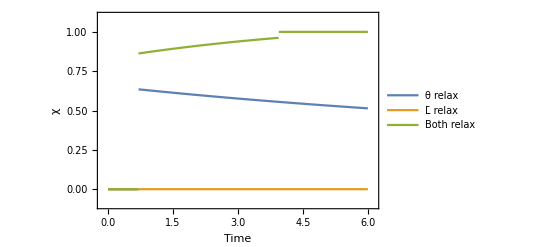

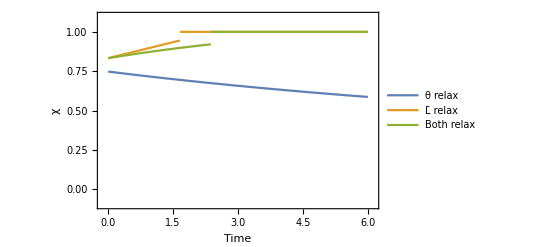

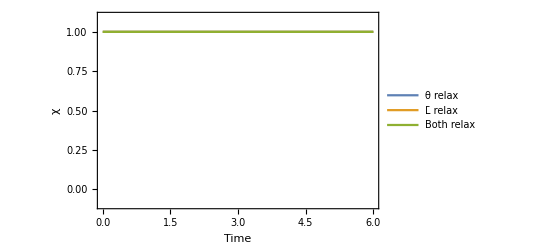

```mathematica
(* More on the mixed/range stuff: The next 4 charts aren't in the paper but trying to understand the new inermediate equilibria *)
```

```mathematica
Manipulate[Plot[Evaluate[{1/βi,RLintBothB,RLbindIntω,1/βp}/.lbar->Lmid/.ω->ωval/.{βi->0.95,βp->0.975,δ->0.012,θ->θval}],{χ,0,1},AxesLabel->{Automatic,Automatic},PlotLegends->{"Upper R","RLintBothB","RLbindIntω", "Lower R"}],{{ωval,0.75},.5,1},{{θval,0.8},.5,1}]
```

```mathematica
Manipulate[Plot[Evaluate[{PLintBothBSolve,pBconO,pBconT,pLconO,pBothconO}/.hO->hbar/.hbar->1/.lbar->Lmid/.ω->ωval/.{βi->0.95,βp->0.975,δ->0.012,θ->θval}],{χ,0,1},AxesLabel->{Automatic,Automatic},PlotLegends->{"PLintBothB","pBconO","pBconT","pLconO","pBothconO"}],{{ωval,0.75},.5,1},{{θval,0.8},.5,1}]
```

```mathematica
Manipulate[Plot[Evaluate[{PLintBothBSolve,LowP,HighP}/.hO->hbar/.hbar->1/.lbar->Lmid/.ω->ωval/.{βi->0.95,βp->0.975,δ->0.012,θ->θval}],{χ,0,1},AxesLabel->{Automatic,Automatic},PlotLegends->{"PLintBothB","Low P","High P"}],{{ωval,0.75},.5,1},{{θval,0.8},.5,1}]
```

```mathematica
(* This is to show how housing consumption is affected *)
Manipulate[Plot[Evaluate[{hTstar,hOstar,χ*hOstar+(1-χ)*hTstar}/.m->p*(1-βp*(1-δ))/βp/.R->RLintBothB/.p->PLintBothBSolve/.lbar->Lmid/.ω->ωval/.{βi->0.95,βp->0.975,δ->0.012,θ->θval}/.hbar->1],{χ,.5,1},AxesLabel->{Automatic,Automatic},PlotLegends->{"hTstar","hOstar","Avg"}],{{ωval,0.75},.5,1},{{θval,0.8},.5,1}]
```

```mathematica
(* 6. Heterogeneous rental aversion*)
```

```mathematica
(* Model the measure of impatient households as having a range of ω. Now the share is determined by the threshold and the system can be closed *)
(* In particualar suppose it is distributed uniformly according to Subscript[ω, j]∼U[w1,w2], with ω1>0. Now anyone with Subscript[ω, j]>indifference threshold will rent and below will own *)
```

```mathematica
(* Non-binding Lbar *)
```

```mathematica
Solve[{ineqOTω,
cO==y-p*hO*(θ*(R-1)+δ),
cT==y-m*hT,
vO'[hO]==(p*(1-βi*(1-δ)-θ*(1-βi*R)))/βi,
vT'[hT]==m/βi,
R==1/βp,
p==(m*βp)/(1-βp*(1-δ)),
hbar==χ*hO+(1-χ)*hT,
χ==(ω-ω1)/(ω2-ω1)},
{cO,cT,hO,hT,p,m,R,χ,ω}]//Simplify
```

$Aborted

```mathematica
(* For some reason it cannot solve this but seems to work fine in two steps
```

```mathematica
{{cOSol,cTSol,hOSol,hTSol,pSol,mSol,RSol,ωSol}}={cO,cT,hO,hT,p,m,R,ω}/.Solve[Evaluate[{ineqOTω,
cO==y-p*hO*(θ*(R-1)+δ),
cT==y-m*hT,
vO'[hO]==(p*(1-βi*(1-δ)-θ*(1-βi*R)))/βi,
vT'[hT]==m/βi,
R==1/βp,
p==(m*βp)/(1-βp*(1-δ)),
hbar==χ*hO+(1-χ)*hT
}],
{cO,cT,hO,hT,p,m,R,ω}]//Simplify
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is βi (-1+βi+Log[ⅇ^((hO p-cO βi+cT βi-«1»-hO p θ+hO p βi θ)/βi)]) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 1-βi-Log[ⅇ^((hO p-cO βi+cT βi-«1»-hO p θ+hO p βi θ)/βi)] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y-(βi (βp (δ-θ)+θ))/(βp+βi βp (-1+δ)+βi θ-βp θ),y-βi,(hbar (-1+βp-βp δ))/(βi θ (-1+χ)-χ+βp (-1+θ+βi (-1+δ) (-1+χ)+2 χ-δ χ-θ χ)),-(hbar (βp+βi βp (-1+δ)+βi θ-βp θ))/(βi θ (-1+χ)-χ+βp (-1+θ+βi (-1+δ) (-1+χ)+2 χ-δ χ-θ χ)),-(βi βp (βi θ (-1+χ)-χ+βp (-1+θ+βi (-1+δ) (-1+χ)+2 χ-δ χ-θ χ)))/(hbar (1+βp (-1+δ)) (βp+βi βp (-1+δ)+βi θ-βp θ)),-(βi (βi θ (-1+χ)-χ+βp (-1+θ+βi (-1+δ) (-1+χ)+2 χ-δ χ-θ χ)))/(hbar (βp+βi βp (-1+δ)+βi θ-βp θ)),1/βp,(ⅇ^(-1+βi) (1+βp (-1+δ)))/(βp+βi βp (-1+δ)+βi θ-βp θ)}}

```mathematica
Simplify[{cOSol,cTSol,hOSol,hTSol,pSol,mSol,RSol,ωSol}/.χ->(ω-ω1)/(ω2-ω1)/.ω->ωSol]//MatrixForm
```

(y-(βi (βp (δ-θ)+θ))/(βp+βi βp (-1+δ)+βi θ-βp θ)
y-βi
(ⅇ hbar (1+βp (-1+δ)) (βp+βi βp (-1+δ)+βi θ-βp θ) (ω1-ω2))/(ⅇ^βi (1+βp (-1+δ)) (-1+βp (2+βi (-1+δ)-δ-θ)+βi θ)+ⅇ (βp+βi βp (-1+δ)+βi θ-βp θ) (ω1+βp (-1+δ) ω1-(βp+βi βp (-1+δ)+βi θ-βp θ) ω2))
-(ⅇ hbar (βp+βi βp (-1+δ)+βi θ-βp θ)^2 (ω1-ω2))/(-ⅇ^βi (1+βp (-1+δ)) (-1+βp (2+βi (-1+δ)-δ-θ)+βi θ)+ⅇ (βp+βi βp (-1+δ)+βi θ-βp θ) ((-1+βp-βp δ) ω1+(βp+βi βp (-1+δ)+βi θ-βp θ) ω2))
(βi βp (ⅇ^βi (1+βp (-1+δ)) (-1+βp (2+βi (-1+δ)-δ-θ)+βi θ)-ⅇ (βp+βi βp (-1+δ)+βi θ-βp θ) ((-1+βp-βp δ) ω1+(βp+βi βp (-1+δ)+βi θ-βp θ) ω2)))/(ⅇ hbar (1+βp (-1+δ)) (βp+βi βp (-1+δ)+βi θ-βp θ)^2 (ω1-ω2))
(ⅇ^βi βi (1+βp (-1+δ)) (-1+βp (2+βi (-1+δ)-δ-θ)+βi θ)-ⅇ βi (βp+βi βp (-1+δ)+βi θ-βp θ) ((-1+βp-βp δ) ω1+(βp+βi βp (-1+δ)+βi θ-βp θ) ω2))/(ⅇ hbar (βp+βi βp (-1+δ)+βi θ-βp θ)^2 (ω1-ω2))
1/βp
(ⅇ^(-1+βi) (1+βp (-1+δ)))/(βp+βi βp (-1+δ)+βi θ-βp θ))

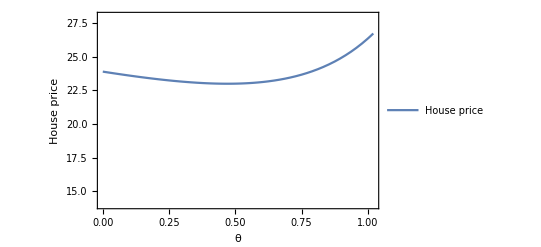

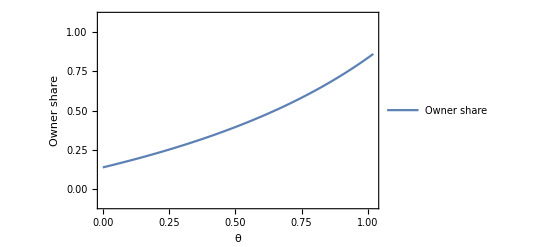

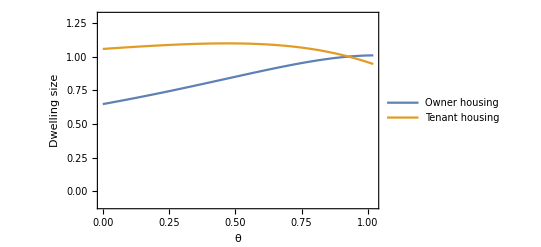

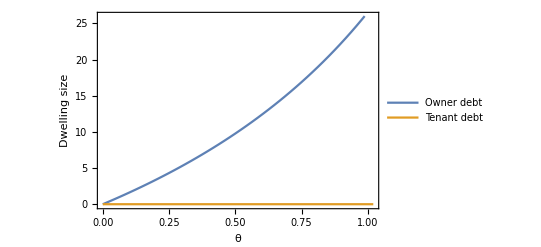

```mathematica
Plot[Evaluate[pSol/.χ->(ω-ω1)/(ω2-ω1)/.ω->ωSol/.JPTparams/.ω1->0.5/.ω2->1.1/.hbar->1],{θ,0.0,1.02},PlotLegends->Placed[{"House price"},Center ],PlotRange->{14,28},Frame->True,FrameLabel->{"θ","House price","House price against θ"}]
Plot[Evaluate[χ/.χ->(ω-ω1)/(ω2-ω1)/.ω->ωSol/.JPTparams/.ω1->0.5/.ω2->1.1/.hbar->1],{θ,0.0,1.02},PlotLegends->Placed[{"Owner share"},Center ],PlotRange->{-.1,1.1},Frame->True,FrameLabel->{"θ","Owner share","χ against θ"},PlotLegends->{"OO share"},AxesLabel->Automatic]
Plot[Evaluate[{hOSol,hTSol}/.χ->(ω-ω1)/(ω2-ω1)/.ω->ωSol/.JPTparams/.ω1->0.5/.ω2->1.1/.hbar->1],{θ,0,1.02},PlotLegends->Placed[{"Owner housing","Tenant housing"},Center ],PlotRange->{-.1,1.3},Frame->True,FrameLabel->{"θ","Dwelling size","House size against θ"}]
Plot[Evaluate[{hOSol*θ*pSol,0}/.χ->(ω-ω1)/(ω2-ω1)/.ω->ωSol/.JPTparams/.ω1->0.5/.ω2->1.1/.hbar->1],{θ,0,1.02},PlotLegends->Placed[{"Owner debt","Tenant debt"},Center ],PlotRange->{-.1,26},Frame->True,FrameLabel->{"θ","Dwelling size","House size against θ"}]
```

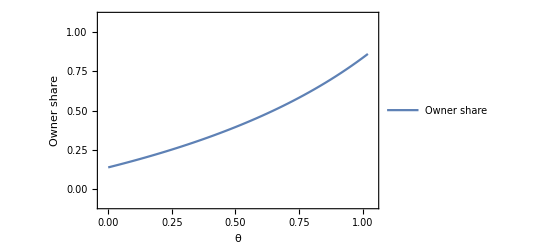

-Graphics-

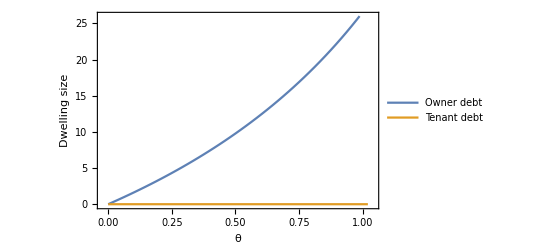

```mathematica
(* Binding Lbar -- this section is incomplete*)
```

```mathematica
Solve[{ineqOTω,
cO==y-p*hO*(θ*(R-1)+δ),
cT==y-m*hT,
vO'[hO]==(p*(1-βi*(1-δ)-θ*(1-βi*R)))/βi,
vT'[hT]==m/βi,
lbar==p*θ*hO*χ,
p==(m*βp)/(1-βp*(1-δ)),
hbar==χ*hO+(1-χ)*hT,χ==(ω-ω1)/(ω2-ω1)},
{cO,cT,hT,p,m,R,χ,ω}]//Simplify
```

$Aborted

```mathematica
Solve[Evaluate[{ineqOT,hO==hOstar}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.m->p*(1-βp*(1-δ))/βp
/.p->lbar/(θ*hO*χ)
/.hbar->hbar],{logω,R}]//Simplify
```

{{logω→-1+βi+Log[hO]-Log[(hO βi βp θ χ)/(lbar+lbar βp (-1+δ))],R→(-1+βi-βi δ+θ)/(βi θ)+χ/lbar}}

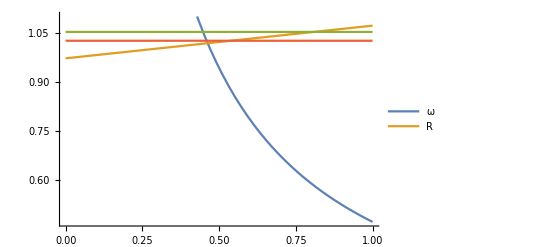

```mathematica
Plot[Evaluate[{Exp[-1+βi+Log[hO]-Log[(hO βi βp θ χ)/(lbar+lbar βp (-1+δ))]],(-1+βi-βi δ+θ)/(βi θ)+χ/lbar,1/βi,1/βp}/.lbar->10/.θ->.8/.JPTparams],{χ,0,1},PlotLegends->{"ω","R"},PlotRange->{1.1,0}]
```

```mathematica
hT==hTstar
```

```mathematica
ineqOT/.hT->hTstar/.p->lbar/(θ*hOstar*χ)//Simplify
```

(hO lbar p (-1+θ) (1-θ+βi (-1+δ+R θ)))/(βi θ χ)+(βi (cT+logω+Log[βi/m]))/(-1+βi)==(βi (cO+Log[hO]))/(-1+βi)

```mathematica
Solve[{ineqOT/.hT->hTstar/.p->lbar/(θ*hOstar*χ),R==(-1+βi-βi δ+θ)/(βi θ)},{logω,R}]//Simplify
```

{{logω→cO-cT+Log[hO]-Log[βi/m],R→(-1+βi-βi δ+θ)/(βi θ)}}

```mathematica
Solve[{lbar/(θ*hOstar*χ)==p,ineqOT,hT==hTstar},{R,logω,m}]//Simplify
```

{{R→(-1+βi-βi δ+θ)/(βi θ)+χ/lbar,logω→cO-cT+hO p-(hO p)/βi-hO p θ+(hO p θ)/βi+Log[hO]-Log[hT],m→βi/hT}}

```mathematica
Solve[lbar/(θ*hOstar*χ)==p,R]//Simplify
```

{{R→(-1+βi-βi δ+θ)/(βi θ)+χ/lbar}}

```mathematica
Reduce[1/βp<(-1+βi-βi δ+θ)/(βi θ)+χ/lbar<1/βi
```

```mathematica
Simplify[Reduce[{1/βp<(-1+βi-βi δ+θ)/(βi θ)+χ/lbar<1/βi},{lbar},Reals],Assumptions->{χ>0,χ<1,βp>0,βi>0,δ>0,δ<1,βp<1,βi<1,lbar>0,θ>0,θ<1,βi<βp,ω>0,ω<1}]
```

(βi θ χ)/(1+βi (-1+δ))<lbar<(βi βp θ χ)/(βp+βi βp (-1+δ)+βi θ-βp θ)

```mathematica
Solve[Evaluate[{ineqOT,hO==hOstar}
/.cO->y-p*hO*(θ*(R-1)+δ)
/.cT ->y-m*hT
/.hT->hTstar
/.m->p*(1-βp*(1-δ))/βp
/.p->lbar/(θ*hO)
/.hO->hbar
/.hbar->hbar],{logω,R}]
```

{{logω→-1+βi+Log[hbar]-Log[(hbar βi βp θ)/(lbar (1-βp (1-δ)))],R→-(lbar-lbar βi+lbar βi δ-lbar θ-βi θ)/(lbar βi θ)}}